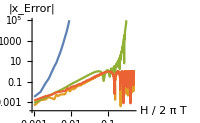
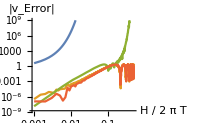
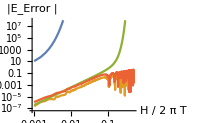
-Graphics- | -Graphics-
-Graphics- |

```mathematica
SetDirectory[NotebookDirectory[]];
d=Import/@FileNames["A_*.dat"];

Grid[{{
ListLinePlot[
Abs@d[[All,All,{1,2}]],
ImageSize->200,PlotRange->{All,10^5},
Ticks->{{0.001,0.01,0.1,0.5},Automatic},
ScalingFunctions->{"Log","Log"},
AxesLabel->{"H / 2 π T","|x_Error|"}
],
ListLinePlot[
Abs@d[[All,All,{1,3}]],
ImageSize->200,PlotRange->{All,10^9},
Ticks->{{0.001,0.01,0.1,0.5},Automatic},
ScalingFunctions->{"Log","Log"},
AxesLabel->{"H / 2 π T","|v_Error|"}
]
},{
ListLinePlot[
Abs@d[[All,All,{1,4}]],
ScalingFunctions->{"Log","Log"},
AxesLabel->{"H / 2 π T","|E_Error |"},
ImageSize->200,PlotRange->{All,10^8},
Ticks->{{0.001,0.01,0.1,0.5},Automatic}
],
LineLegend[ColorData[97,"ColorList"],Style[#,11]&/@{"explizites Euler Verfahren","Leap Frog Verfahren", "Runge Kutta Verfahren\n(2.Ordnung)","Verlet Verfahren" }]
}}]
Export["A_plot.pdf",%];
```

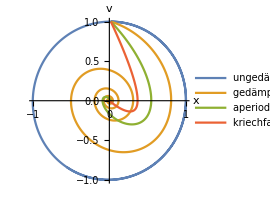

```mathematica
SetDirectory[NotebookDirectory[]];
d=Import/@FileNames["B_*.dat"];
ListLinePlot[d[[All,All,{2,3}]],PlotRange->All,AspectRatio->Automatic,ImageSize->200,AxesLabel->{"x","v"},
PlotLegends->Placed[Style[#,11]&/@{"ungedämpft γ=0","gedämpft γ=0.3","aperiodischer Grenzfall γ=1","kriechfall γ=2"},Below]
]
Export["B_Phase.pdf",%];
```

```mathematica
SetDirectory[NotebookDirectory[]];
d=Import@FileNames["C_*.dat"][[1]];
d=DeleteCases[d, {}];
ByteCount@d

Row[{
ListDensityPlot[d[[All,{1,2,3}]],PlotLegends->BarLegend[Automatic,LegendMarkerSize->180],ColorFunction->"SunsetColors",PlotLabel->"Amplitude",FrameLabel->{"γ","ω_t/ω_E"},PlotRange->{{0.05,5},All,{0,5}},ScalingFunctions->"SignedLog",ImageSize->200,
MeshFunctions->{#3&},Mesh->15,MeshStyle->White
],
ListDensityPlot[#-{0,0,Pi}&/@d[[All,{1,2,4}]],PlotLegends->BarLegend[Automatic,LegendMarkerSize->180],ColorFunction->Hue,PlotLabel->"Phasenverschiebung",FrameLabel->{"γ","ω_t/ω_E"},ImageSize->200,PlotRange->{{0.05,5},All,{-Pi,Pi}},
MeshFunctions->{#3&},Mesh->0,MeshStyle->White
]
 }
]
Export["C_Plot.pdf",%,RasterSize->1000];
```

5299280

-Graphics--Graphics-

```mathematica
ListPlot3D[d[[All,{1,2,3}]],ColorFunction->"SunsetColors",AxesLabel->{"γ","ω_t/ω_E","A/A_t"},PlotRange->{{0.05,5},{0.05,All},{0,5}},Boxed->False,MeshFunctions->{#3&},MeshStyle->White,Mesh->15,MaxPlotPoints->200,PlotLegends->BarLegend[Automatic,LegendMarkerSize->180]
]
Export["C_3D.pdf",%,RasterSize->1000];
```

-Graphics3D-

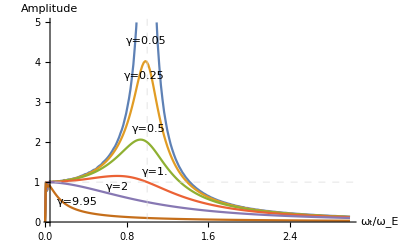

```mathematica
ListLinePlot[
Evaluate@Table[Select[d[[All,{1,2,3}]],#[[1]]==i&][[All,{2,3}]],{i,{0.05,0.25,0.5,1.0,2,9.95}}],PlotRange->{{0.05,All},{0,5}},AxesLabel->{"ω_t/ω_E","Amplitude"},
PlotLabels->{Placed["γ=0.05",1.17],Placed["γ=0.25",1],Placed["γ=0.5",1],Placed["γ=1.",1],Placed["γ=2",{.7,0.68}],Placed["γ=9.95",{.3,0.325}]},
GridLines->{{1},{1}},GridLinesStyle->Dashed
]
Export["C_Seite.pdf",%];
```